### Imports

```mathematica
(* kill everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\Tal Miller\\Dropbox\\UNI\\Courses Graduate\\QFT\\Papers and Reviews\\Supersymmetric index and Localization\\Thesis\\Notebooks\\Star_shaped_quivers"];
```

```mathematica
<<"CharactersFunctions.m"
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\11.0\\AddOns\\Applications\\LieART\\LieART.m"]
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
maxVarNum=6;
a=Table[Subscript["a",i],{i,maxVarNum}];
b=Table[Subscript["b",i],{i,maxVarNum}];
$Assumptions={r>0,r<1};
```

### Sp(4) chars

#### Rep {1,0} (fundamental)

```mathematica
algebraClass=C;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+1/a_2+1/a_1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r/a_1) (1-a_1 r) (1-r/a_2) (1-a_2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.046875 seconds = 0.0000130208 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

Numeric divergence degree is 0.

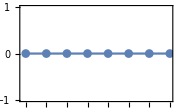

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,0} + Rep {1,0}

```mathematica
algebraClass=C;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+1/a_2+1/a_1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r/a_1)^2 (1-a_1 r)^2 (1-r/a_2)^2 (1-a_2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.078125 seconds = 0.0000217014 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

Numeric divergence degree is -0.998006

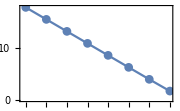

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {0,1}

```mathematica
algebraClass=C;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

5

a_2 a_1+a_1/a_2+a_2/a_1+1/(a_2 a_1)+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-a_1 a_2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is zero.

Residue for pole 2/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.140625 seconds = 0.0000390625 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^3)

Numeric divergence degree is -0.996046

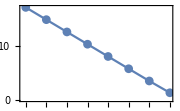

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {0,1} + Rep {0,1}

```mathematica
algebraClass=C;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

5

a_2 a_1+a_1/a_2+a_2/a_1+1/(a_2 a_1)+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r)^2 (1-r/(a_1 a_2))^2 (1-(a_1 r)/a_2)^2 (1-(a_2 r)/a_1)^2 (1-a_1 a_2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is zero.

Residue for pole 2/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.265625 seconds = 0.0000737847 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^3)

Numeric divergence degree is -2.99402

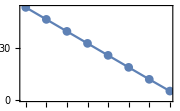

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0} (adjoint)

```mathematica
algebraClass=C;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_1/a_2+a_2^2+1/a_2^2+a_2/a_1+1/(a_2 a_1)+1/a_1^2+2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r)^2 (1-r/a_1^2) (1-a_1^2 r) (1-r/a_2^2) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-a_1 a_2 r) (1-a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 3/5 in level 1 is zero.

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

calculation time = 0.875 seconds = 0.000243056 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/((r^2-1)^2 (r^2+1))

Numeric divergence degree is -1.99213

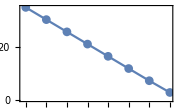

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {0,2}

```mathematica
algebraClass=C;
repDynkinLabels={0,2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

14

a_2^2 a_1^2+a_1^2/a_2^2+a_1^2+a_2 a_1+a_1/a_2+a_2^2+1/a_2^2+a_2/a_1+1/(a_2 a_1)+a_2^2/a_1^2+1/(a_2^2 a_1^2)+1/a_1^2+2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r)^2 (1-r/a_1^2) (1-a_1^2 r) (1-r/a_2^2) (1-r/(a_1^2 a_2^2)) (1-(a_1^2 r)/a_2^2) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-a_1 a_2 r) (1-a_2^2 r) (1-(a_2^2 r)/a_1^2) (1-a_1^2 a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 1

Calculating residue for pole 2/9 in level 1

Calculating residue for pole 3/9 in level 1

Calculating residue for pole 4/9 in level 1

Calculating residue for pole 5/9 in level 1

Calculating residue for pole 6/9 in level 1

Calculating residue for pole 7/9 in level 1

Calculating residue for pole 8/9 in level 1

Calculating residue for pole 9/9 in level 1

Residue for pole 1/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 2/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 3/9 in level 1 is zero.

Residue for pole 4/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 5/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 6/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 12

Calculating residue for pole 1/12 in level 2

Calculating residue for pole 2/12 in level 2

Calculating residue for pole 3/12 in level 2

Calculating residue for pole 4/12 in level 2

Calculating residue for pole 5/12 in level 2

Calculating residue for pole 6/12 in level 2

Calculating residue for pole 7/12 in level 2

Calculating residue for pole 8/12 in level 2

Calculating residue for pole 9/12 in level 2

Calculating residue for pole 10/12 in level 2

Calculating residue for pole 11/12 in level 2

Calculating residue for pole 12/12 in level 2

Residue for pole 7/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 8/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 9/9 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

calculation time = 4.39063 seconds = 0.00121962 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/((r-1)^4 (r+1)^2 (r^2+1) (r^2+r+1) (r^4+r^3+r^2+r+1))

Numeric divergence degree is -3.9804

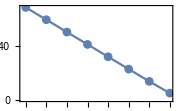

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,1}

```mathematica
algebraClass=C;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

16

a_2 a_1^2+a_1^2/a_2+a_2^2 a_1+a_1/a_2^2+2 a_1+2 a_2+2/a_2+a_2^2/a_1+1/(a_2^2 a_1)+2/a_1+a_2/a_1^2+1/(a_2 a_1^2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r/a_1)^2 (1-a_1 r)^2 (1-r/(a_1 a_2^2)) (1-(a_1 r)/a_2^2) (1-r/a_2)^2 (1-r/(a_1^2 a_2)) (1-(a_1^2 r)/a_2) (1-a_2 r)^2 (1-(a_2 r)/a_1^2) (1-a_1^2 a_2 r) (1-(a_2^2 r)/a_1) (1-a_1 a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 2/8 in level 1 is zero.

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 14

Calculating residue for pole 1/14 in level 2

Calculating residue for pole 2/14 in level 2

Calculating residue for pole 3/14 in level 2

Calculating residue for pole 4/14 in level 2

Calculating residue for pole 5/14 in level 2

Calculating residue for pole 6/14 in level 2

Calculating residue for pole 7/14 in level 2

Calculating residue for pole 8/14 in level 2

Calculating residue for pole 9/14 in level 2

Calculating residue for pole 10/14 in level 2

Calculating residue for pole 11/14 in level 2

Calculating residue for pole 12/14 in level 2

Calculating residue for pole 13/14 in level 2

Calculating residue for pole 14/14 in level 2

Residue for pole 4/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Residue calculation failed.

Failed residue exists in level 2, return "failed" flag

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Residue calculation failed.

Failed residue exists in level 2, return "failed" flag

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Accumulated sick branches {4,5}/8 in level1

Summing and simplifying the sick branches.

Resending to level2

Level = 2

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 2

Calculating residue for pole 2/7 in level 2

Calculating residue for pole 3/7 in level 2

Calculating residue for pole 4/7 in level 2

Calculating residue for pole 5/7 in level 2

Calculating residue for pole 6/7 in level 2

Calculating residue for pole 7/7 in level 2

Forming a new list of healty branches in level 1

calculation time = 50.3594 seconds = 0.0139887 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

$Aborted

Numeric divergence degree is -5.97785

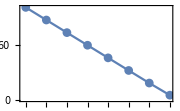

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {3,0}

```mathematica
algebraClass=C;
repDynkinLabels={3,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

20

a_1^3+a_2 a_1^2+a_1^2/a_2+a_2^2 a_1+a_1/a_2^2+2 a_1+a_2^3+2 a_2+2/a_2+1/a_2^3+a_2^2/a_1+1/(a_2^2 a_1)+2/a_1+a_2/a_1^2+1/(a_2 a_1^2)+1/a_1^3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 (1-r/a_1^3) (1-r/a_1)^2 (1-a_1 r)^2 (1-a_1^3 r) (1-r/a_2^3) (1-r/(a_1 a_2^2)) (1-(a_1 r)/a_2^2) (1-r/a_2)^2 (1-r/(a_1^2 a_2)) (1-(a_1^2 r)/a_2) (1-a_2 r)^2 (1-(a_2 r)/a_1^2) (1-a_1^2 a_2 r) (1-(a_2^2 r)/a_1) (1-a_1 a_2^2 r) (1-a_2^3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 1

Calculating residue for pole 2/11 in level 1

Calculating residue for pole 3/11 in level 1

Calculating residue for pole 4/11 in level 1

Calculating residue for pole 5/11 in level 1

Calculating residue for pole 6/11 in level 1

Calculating residue for pole 7/11 in level 1

Calculating residue for pole 8/11 in level 1

Calculating residue for pole 9/11 in level 1

Calculating residue for pole 10/11 in level 1

Calculating residue for pole 11/11 in level 1

Residue for pole 1/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 2/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 3/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 4/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 5/11 in level 1 is zero.

Residue for pole 6/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 26

Calculating residue for pole 1/26 in level 2

Calculating residue for pole 2/26 in level 2

Calculating residue for pole 3/26 in level 2

Calculating residue for pole 4/26 in level 2

Calculating residue for pole 5/26 in level 2

Calculating residue for pole 6/26 in level 2

Calculating residue for pole 7/26 in level 2

Calculating residue for pole 8/26 in level 2

Calculating residue for pole 9/26 in level 2

Calculating residue for pole 10/26 in level 2

Calculating residue for pole 11/26 in level 2

Calculating residue for pole 12/26 in level 2

Calculating residue for pole 13/26 in level 2

Calculating residue for pole 14/26 in level 2

Calculating residue for pole 15/26 in level 2

Calculating residue for pole 16/26 in level 2

Calculating residue for pole 17/26 in level 2

Calculating residue for pole 18/26 in level 2

Calculating residue for pole 19/26 in level 2

Calculating residue for pole 20/26 in level 2

Calculating residue for pole 21/26 in level 2

Calculating residue for pole 22/26 in level 2

Calculating residue for pole 23/26 in level 2

Calculating residue for pole 24/26 in level 2

Calculating residue for pole 25/26 in level 2

Calculating residue for pole 26/26 in level 2

Residue for pole 7/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 14

Calculating residue for pole 1/14 in level 2

Calculating residue for pole 2/14 in level 2

Calculating residue for pole 3/14 in level 2

Residue calculation failed.

Failed residue exists in level 2, return "failed" flag

Residue for pole 8/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 14

Calculating residue for pole 1/14 in level 2

Calculating residue for pole 2/14 in level 2

Calculating residue for pole 3/14 in level 2

Residue calculation failed.

Failed residue exists in level 2, return "failed" flag

Residue for pole 9/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 2

Calculating residue for pole 2/11 in level 2

Calculating residue for pole 3/11 in level 2

Calculating residue for pole 4/11 in level 2

Calculating residue for pole 5/11 in level 2

Calculating residue for pole 6/11 in level 2

Calculating residue for pole 7/11 in level 2

Calculating residue for pole 8/11 in level 2

Calculating residue for pole 9/11 in level 2

Calculating residue for pole 10/11 in level 2

Calculating residue for pole 11/11 in level 2

Residue for pole 10/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 2

Calculating residue for pole 2/11 in level 2

Calculating residue for pole 3/11 in level 2

Calculating residue for pole 4/11 in level 2

Calculating residue for pole 5/11 in level 2

Calculating residue for pole 6/11 in level 2

Calculating residue for pole 7/11 in level 2

Calculating residue for pole 8/11 in level 2

Calculating residue for pole 9/11 in level 2

Calculating residue for pole 10/11 in level 2

Calculating residue for pole 11/11 in level 2

Residue for pole 11/11 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Accumulated sick branches {7,8}/11 in level1

Summing and simplifying the sick branches.

Resending to level2

Level = 2

Number of relevant poles = 13

Calculating residue for pole 1/13 in level 2

Calculating residue for pole 2/13 in level 2

Calculating residue for pole 3/13 in level 2

Calculating residue for pole 4/13 in level 2

Calculating residue for pole 5/13 in level 2

Calculating residue for pole 6/13 in level 2

Calculating residue for pole 7/13 in level 2

Calculating residue for pole 8/13 in level 2

Calculating residue for pole 9/13 in level 2

Calculating residue for pole 10/13 in level 2

Calculating residue for pole 11/13 in level 2

Calculating residue for pole 12/13 in level 2

Calculating residue for pole 13/13 in level 2

Forming a new list of healty branches in level 1

calculation time = 63.1719 seconds = 0.0175477 hours

Numeric divergence degree is -9.97892

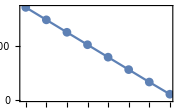

```mathematica
calcNumericDivergence[hilbertComponents]
```

### Sp(4) + U(1) chars

#### Sp(4) rep {1,0} + rep {1,0} with opposite U(1) charges

```mathematica
algebraClass=C;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+1/a_2+1/a_1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 t (1-r/(a_1 t)) (1-(r t)/a_1) (1-(a_1 r)/t) (1-a_1 r t) (1-r/(a_2 t)) (1-(r t)/a_2) (1-(a_2 r)/t) (1-a_2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

calculation time = 1.04688 seconds = 0.000290799 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### Sp(4) rep {0,1} + singlet with opposite U(1) charges

```mathematica
algebraClass=C;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

5

a_2 a_1+a_1/a_2+a_2/a_1+1/(a_2 a_1)+1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 t (1-r/t) (1-r t) (1-(r t)/(a_1 a_2)) (1-(a_1 r t)/a_2) (1-(a_2 r t)/a_1) (1-a_1 a_2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 1/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.234375 seconds = 0.0000651042 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^4)

Numeric divergence degree is -0.994119

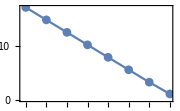

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Sp(4) rep {0,1} + rep {0,1} with opposite U(1) charges

```mathematica
algebraClass=C;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

5

a_2 a_1+a_1/a_2+a_2/a_1+1/(a_2 a_1)+1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 t (1-r/t) (1-r t) (1-r/(a_1 a_2 t)) (1-(r t)/(a_1 a_2)) (1-(a_1 r)/(a_2 t)) (1-(a_1 r t)/a_2) (1-(a_2 r)/(a_1 t)) (1-(a_2 r t)/a_1) (1-(a_1 a_2 r)/t) (1-a_1 a_2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 1

Calculating residue for pole 2/6 in level 1

Calculating residue for pole 3/6 in level 1

Calculating residue for pole 4/6 in level 1

Calculating residue for pole 5/6 in level 1

Calculating residue for pole 6/6 in level 1

Residue for pole 1/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 1/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 2/6 in level 1 is zero.

Residue for pole 3/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 5/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 6/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 1.3125 seconds = 0.000364583 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/((r^2-1)^2 (r^2+1))

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -1.99213

-Graphics-

#### Sp(4) rep {2,0} + singlet with opposite U(1) charges

```mathematica
algebraClass=C;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_1/a_2+a_2^2+1/a_2^2+a_2/a_1+1/(a_2 a_1)+1/a_1^2+2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1^2) (1-a_1/a_2) (1-a_1 a_2) (1-a_2^2))/(a_1 a_2 t (1-r/t) (1-r t)^2 (1-(r t)/a_1^2) (1-a_1^2 r t) (1-(r t)/a_2^2) (1-(r t)/(a_1 a_2)) (1-(a_1 r t)/a_2) (1-(a_2 r t)/a_1) (1-a_1 a_2 r t) (1-a_2^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/2 in level 1 is zero.

calculation time = 1.07813 seconds = 0.000299479 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/((r^4-1)^2 (r^4+1))

Numeric divergence degree is -1.98086

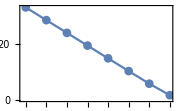

```mathematica
calcNumericDivergence[hilbertComponents]
```